## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation/fake-spectra

```mathematica
Get["../../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
spectFunLinear[u_]:=u+0.5;
```

```mathematica
linearDRMAADataRaw=Import["okMAAdata-linear-01.csv"];
linearDRMZApDataRaw=Import["okMZApdata-linear-01.csv"];
linearDRMZAmDataRaw=Import["okMZAmdata-linear-01.csv"];
```

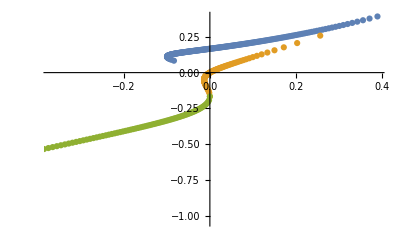

```mathematica
ListPlot[{{-#[[1]],-#[[2]]}&/@linearDRMAADataRaw,{-#[[1]],-#[[2]]}&/@linearDRMZApDataRaw,{-#[[1]],-#[[2]]}&/@linearDRMZAmDataRaw}]
```

## Clean Up Data

```mathematica
maalsadataLinear01=Import[
"/Users/leima/github/dispersion-relation-paper/program/data/linear/maalsadata-linear-01.csv"
];
mzaplsadataLinear01=Import[
"/Users/leima/github/dispersion-relation-paper/program/data/linear/mzaplsadata-linear-01.csv"
];
mzamlsadataLinear01=Import[
"/Users/leima/github/dispersion-relation-paper/program/data/linear/mzamlsadata-linear-01.csv"
];
```

```mathematica
Dimensions@maalsadataLinear01
Dimensions@mzaplsadataLinear01
Dimensions@mzamlsadataLinear01
```

{8999,3}

{900,3}

{900,3}

```mathematica
maalsadataLinear01Clean=Select[
maalsadataLinear01,10^(-10)<Abs@#[[3]]<20&&-5<#[[2]]<0&
];
Dimensions@%

mzaplsadataLinear01Clean=Select[
mzaplsadataLinear01,10^(-10)<Abs@#[[3]]<10&&#[[1]]<0&
];

Dimensions@%

mzamlsadataLinear01Clean=Select[
mzamlsadataLinear01,10^(-10)<Abs@#[[3]]<10&&#[[1]]>0&
];

Dimensions@%
```

{138,3}

{118,3}

{112,3}

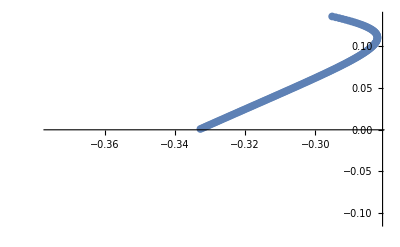

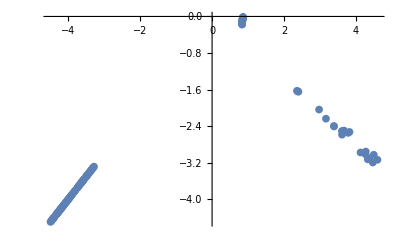

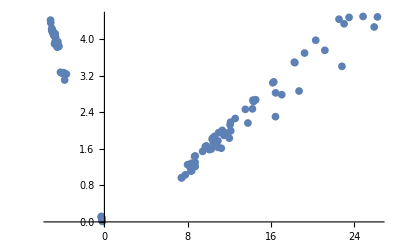

```mathematica
ListPlot[
{#[[2]],#[[1]]}&/@maalsadataLinear01Clean
]
ListPlot[
{#[[2]],#[[1]]}&/@mzaplsadataLinear01Clean
]
ListPlot[
{#[[2]],#[[1]]}&/@mzamlsadataLinear01Clean
]
```

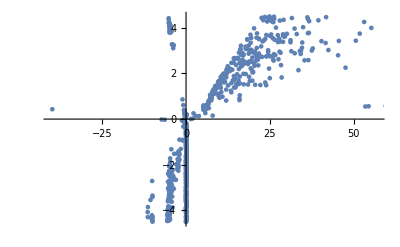

```mathematica
ListPlot[
{#[[2]],#[[1]]}&/@mzamlsadataLinear01
]
```

```mathematica
valepsilon=0.001
```

0.001

```mathematica
maalsadataLinear01Clean=Select[maalsadataLinear01,
(Abs@SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFunLinear])<valepsilon&
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.00387517}. NIntegrate obtained -17.9961 - 8.07938×10^-16\ ⅈ and 19.0046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.00387517}. NIntegrate obtained -17.9921 - 4.22935×10^-17\ ⅈ and 19.0004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.00387517}. NIntegrate obtained -17.988 - 2.00007×10^-17\ ⅈ and 17.9879 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{}